## Preamble & prep

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->16,FontColor->Black};
```

```mathematica
exportImages=True;
ExportToIMGFolder[cmd_,filename_]:=Module[{result},
result=cmd;
If[exportImages,Export[StringJoin[ParentDirectory@NotebookDirectory[],"/tex/pictures/"]<>filename<>".svg",result,"SVG"],Null];
result]
```

```mathematica
<<xAct`xCoba`
<<xAct`ShowTime1`
$RecursionLimit=Infinity;
Off[General::spell]
$DefInfoQ=False;
$CVVerbose=False;
$xCobaCacheVerbose=False;
$PrePrint=ScreenDollarIndices;
$Post=ScreenDollarIndices;
$CVSimplify=Together;
$CVReplace=False;
$CovDFormat="Postfix";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## xAct setup of Schwarzschild spacetime

Setting up the charts

```mathematica
DefManifold[M4,4,{μ,ν,α,β,σ}]
```

```mathematica
DefConstantSymbol[M]
```

```mathematica
DefChart[schw,M4, Range[0,3], {t[],r[],θ[],ϕ[]},FormatBasis->{"Partials","Differentials"},ChartColor->Red]
```

```mathematica
$Assumptions=And[
(t[]|r[]|θ[]|ϕ[])∈Reals,
2M>r[]>0,
0<=ϕ[],
M>0
];
```

```mathematica
gschw = CTensor[DiagonalMatrix[{-(1-(2M)/r[]),(1-(2M)/r[])^-1,r[]^2,(r[] Sin[θ[]])^2}],{-schw,-schw},0]
```

CTensor[{{-1+(2 M)/r,0,0,0},{0,1/(1-(2 M)/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-schw,-schw},0]

```mathematica
SetCMetric[gschw,schw,SignatureOfMetric->{3,1,0}]
```

```mathematica
ToCTensor[gschw,{-schw,-schw}][-α,-β]
```

-1+(2 M)/r | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2 |   |  
α | β

```mathematica
CDschw=CovDOfMetric[gschw]//FullSimplify;
```

```mathematica
MetricCompute[gschw,schw,All]//AbsoluteTiming
```

{0.046831,Null}

```mathematica
Christoffel[CDschw,PDschw][α,-β,-δ]//FullSimplify
```

0
M/(r (-2 M+r))
0
0 | M/(r (-2 M+r))
0
0
0 | 0
0
0
0 | 0
0
0
0
(M (-2 M+r))/r^3
0
0
0 | 0
M/(2 M r-r^2)
0
0 | 0
0
2 M-r
0 | 0
0
0
(2 M-r) Sin[θ]^2
0
0
0
0 | 0
0
1/r
0 | 0
1/r
0
0 | 0
0
0
-Cos[θ] Sin[θ]
0
0
0
0 | 0
0
0
1/r | 0
0
0
Cot[θ] | 0
1/r
Cot[θ]
0 | α |   |  
  | β | δ

```mathematica
Riemann[CDschw][-α,-β,-δ,σ]//FullSimplify
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 M (2 M-r))/r^4 | 0 | 0
-(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4 | 0
0 | 0 | 0 | 0
M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M Sin[θ]^2)/r | 0 | 0 | 0
0 | (2 M (-2 M+r))/r^4 | 0 | 0
(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/((2 M-r) r^2) | 0
0 | M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/((2 M-r) r^2)
0 | 0 | 0 | 0
0 | (M Sin[θ]^2)/r | 0 | 0
0 | 0 | (M (2 M-r))/r^4 | 0
0 | 0 | 0 | 0
-M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/(r^2 (-2 M+r)) | 0
0 | -M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 M)/r
0 | 0 | -(2 M Sin[θ]^2)/r | 0
0 | 0 | 0 | (M (2 M-r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/(r^2 (-2 M+r))
0 | 0 | 0 | 0
0 | -(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 M)/r
0 | 0 | (2 M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   | σ
α | β | δ |

```mathematica
Ricci[CDschw][-α,-β]//FullSimplify
```

0

## Numerical calculations of geodesic equation

Now that we’re done with the charts, it’s time to create some curves. We’ll start with geodesics, and focus on purely radial infall first.

```mathematica
DefParameter[λ]
DefParameter[τ]
```

```mathematica
DefConstantSymbol[amag]
```

```mathematica
DefScalarFunction/@{γt,γr,γϕ,at,ar,aϕ,e,L}
```

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
x={γt[λ],γr[λ],π/2,γϕ[λ]}
u=CTensor[D[x,λ],{schw},0]
a = CTensor[ {at[λ],ar[λ],0,aϕ[λ]},{schw},0]
```

{γt[λ],γr[λ],π/2,γϕ[λ]}

CTensor[{γt'[λ],γr'[λ],0,γϕ'[λ]},{schw},0]

CTensor[{at[λ],ar[λ],0,aϕ[λ]},{schw},0]

```mathematica
plane={θ[]->π/2}
```

{θ→π/2}

```mathematica
constants=Flatten@{Solve[u[-ν]  CTensor[{0,0,0,1},{schw},0][ν]==L[λ]/.plane,γϕ'[λ]],Solve[u[-ν] CTensor[{1,0,0,0},{schw},0][ν]==e[λ]//FullSimplify,γt'[λ]]}
```

{γϕ'[λ]→L[λ]/r^2,γt'[λ]→-(e[λ] r)/(-2 M+r)}

```mathematica
u[μ]/.constants//FullSimplify
```

(e[λ] r)/(2 M-r)
γr'[λ]
0
L[λ]/r^2 | μ

```mathematica
unorm=First@Simplify@Solve[u[α]u[-α]==-1/.plane,γr'[λ]]
anorm=Simplify@Solve[a[α] a[-α]==amag^2/.plane,at[λ]]
aunorm=First@Simplify@Solve[a[α] u[-α]==0/.plane,ar[λ]]
```

{γr'[λ]→-(√((2 M-r) (r+(2 M-r) γt'[λ]^2+r^3 γϕ'[λ]^2)))/r}

{{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(-2 M+r)},{at[λ]→√((r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2)))/(-2 M+r)^2)}}

{ar[λ]→((2 M-r) (at[λ] (2 M-r) γt'[λ]+aϕ[λ] r^3 γϕ'[λ]))/(r^2 γr'[λ])}

```mathematica
Solve[First[(anorm/.aunorm/.unorm/.{at[λ]->0,γt'[λ]->0}//FullSimplify)/.{Rule->Equal}],aϕ[λ]]
```

{{aϕ[λ]→-(amag √(1+r^2 γϕ'[λ]^2))/r},{aϕ[λ]→(amag √(1+r^2 γϕ'[λ]^2))/r}}

```mathematica
unorm/.constants//Simplify
```

{γr'[λ]→-(√(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/r}

```mathematica
eqOfMotion =ParamD[λ][u[α]]+Christoffel[CDschw,PDschw][α,-β,-δ]u[β]u[δ]-a[α]
```

●
●
-Cos[θ] Sin[θ] γϕ'[λ]^2
-aϕ[λ]+(2 γr'[λ] γϕ'[λ])/r+γϕ''[λ] | α

## Calculation functions

```mathematica
solveEquations[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,λrange_List,assumptions_,plotfunc_:γt,debug_:False]:=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},λrange]];
If[debug,
Print[Simplify/@{unorm,constants,eqs}];
Print[Simplify@(eqTable/.unorm)/.r[]->γr[λ]/.M->mass];
Print[ustart];
Print[aeqs];
Print[system//Simplify];
Print[solution];
];
Return[{ParametricPlot[{γr[λ],plotfunc[λ](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,BaseStyle->texStyle,LabelStyle->texStyle],
ParametricPlot[{γr[λ] * Cos[plotfunc[λ]],γr[λ] * Sin[plotfunc[λ]](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1,BaseStyle->texStyle],
ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Boxed->False,BaseStyle->texStyle],
system,
{{γr[λ],plotfunc[λ](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]}
}]
];
```

```mathematica
DisplayCartesianTPlots[plots_,labels_:{},positive_:False,M_:1]:=Module[{},
Show[
Plot[
{0},
{r,0,2M},
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotStyle->None,
GridLines->{{{1M,Directive[Gray,Thin,Dashed]},{2M,Directive[Black,Thick]}},ResourceFunction["CartesianProduct"][Range[If[positive,0,-20],20,10],{Directive[Gray,Thin,Dashed]}]},
Axes->{True,True},
AxesLabel->{MaTeX["r",Magnification->1.1], MaTeX["t",Magnification->1.1]},
AxesStyle->{Directive[Thickness[-2]],Directive[Black,Thick]},
AxesOrigin->{0,If[positive,0,-25]},
BaseStyle->texStyle,
LabelStyle->texStyle,
Ticks->{{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}},({#,MaTeX[#,Magnification->1.1]})&/@Range[If[positive,0,-20],20,10]}],
plots,
labels,
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotLabels->Automatic,
LabelStyle->texStyle,
ImageSize->Large,
TicksStyle->texStyle
]
]
DisplayCartesianPhiPlots[plots_,labels_:{},positive_:False,M_:1]:=Module[{},
Show[
Plot[
{0},
{r,0,2M},
PlotRange->{{0,2.05M},{If[positive,-0.02π,-1.02π],1.02π}},
PlotStyle->None,
GridLines->{{{1M,Directive[Gray,Thin,Dashed]},{2M,Directive[Black,Thick]}},ResourceFunction["CartesianProduct"][Range[If[positive,0,-π],π,π/4],{Directive[Gray,Thin,Dashed]}]},
Axes->{True,True},
AxesLabel->MaTeX/@{"r", "\\phi"},
AxesStyle->{Directive[Thickness[-2]],Automatic},
AxesOrigin->{0,If[positive,0,-π]},
BaseStyle->texStyle,
LabelStyle->texStyle,
Ticks->{{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}},Range[If[positive,0,-π],π,π/2]}],
plots,
labels,
PlotRange->{{0,2.05M},{If[positive,-0.02π,-1.02π],1.02π}},
ImageSize->Large,
LabelStyle->texStyle
]
]
```

```mathematica
Options[colorPolarAxes]={PolarAxesStyle->{},PolarLabelsStyle->{},PolarTicksStyle->{}};
colorPolarAxes[plot_Graphics,OptionsPattern[]]:=ReplaceAll[plot,{Text[Style[lbl__,{}],pos__]:>Text[Style[lbl,OptionValue[PolarLabelsStyle]],pos],Style[Line[def__],{}]:>Style[Line[def],OptionValue[PolarTicksStyle]],Circle[options__]:>Style[Circle[options],OptionValue[PolarAxesStyle]]}]
DisplayPolarPhiPlots[plots_,labels_:{},M_:1]:=Module[{},
Show[
colorPolarAxes[PolarPlot[
{2},
{r,0,2M},
PlotStyle->None,
PolarGridLines->{
ResourceFunction["CartesianProduct"][Range[0,2π,π/6],{Directive[Gray,Thick,Dashed]}],{{1M,Directive[Gray,Thick,Dashed]},{2M,Directive[Black,Thick]}}
},
PolarAxes->True,
PolarAxesOrigin->{0,2M},
PolarTicks->{({#,MaTeX[#,Magnification->1.1]})&/@Range[0,2 π-π/6,π/6],{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}}},
PlotRangeClipping->False,
PlotRangePadding->.1,
LabelStyle->texStyle,
BaseStyle->texStyle
],
PolarLabelsStyle->texStyle],
plots,
labels,
PlotRange->Automatic,
ImageSize->Large
]
]
```

```mathematica
solveEquationsUpToBestGeodesic[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,λrange_List,assumptions_,plotfunc_:γt,debug_:False]:=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution,root,rootVals,solutionFall,solutionCombined,constantEqs},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},λrange]];
root=Re@First@Values@FindRoot[plotfunc'[λ]/.solution,{λ,0}];
rootVals={γt[root]==N[γt[root]/.solution][[1]],γr[root]==N[γr[root]/.solution][[1]],γϕ[root]==N[γϕ[root]/.solution][[1]],plotfunc'[root]==0,γr'[root]==N[γr'[root]/.solution][[1]]};
solutionFall=NDSolve[Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,rootVals]/.Rule->Equal/.{M->mass,amag->0},{γt,γr,γϕ},Join[{λ,root},{λrange[[2]]}]];
solutionCombined=
{
γt->Function[Piecewise[{{γt[#]/.solution,# <= root},{γt[#]/.solutionFall, # > root}}]],
γr->Function[Piecewise[{{γr[#]/.solution,# <= root},{γr[#]/.solutionFall, # > root}}]],
γϕ->Function[Piecewise[{{γϕ[#]/.solution,# <= root},{γϕ[#]/.solutionFall, # > root}}]]
};
constantEqs=(Solve[constants/.Rule->Equal,{e[λ],L[λ]}]/.r[]->γr[λ]//Simplify);
If[debug,
Print[Simplify/@{unorm,constants,eqs}];
Print[Simplify@(eqTable/.unorm)/.r[]->γr[λ]/.M->mass];
Print[ustart];
Print[aeqs];
Print[system//Simplify];
Print[solution];
Print[root];
Print[rootVals];
Print[solutionFall];
Print[solutionCombined];
Print[constantEqs];
];
Return[{ParametricPlot[{γr[λ],plotfunc[λ]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,Exclusions->None,BaseStyle->texStyle],
ParametricPlot[{γr[λ] * Cos[plotfunc[λ]],γr[λ] * Sin[plotfunc[λ]]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1,Exclusions->None,BaseStyle->texStyle],
ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Exclusions->None,BaseStyle->texStyle],
system,
ParametricPlot[({{γr[λ],e[λ]},{γr[λ],L[λ]}(*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.constantEqs[[1]]//Simplify)/.solutionCombined/.M->mass,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,Exclusions->None,PlotStyle->{Blue,Orange},Evaluated->True,BaseStyle->texStyle]
}]
];
```

## Graphs of geodesic equation numerically

NDSolve::ndsz: At λ == 1.33031, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.78367, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.13544, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

11.4711

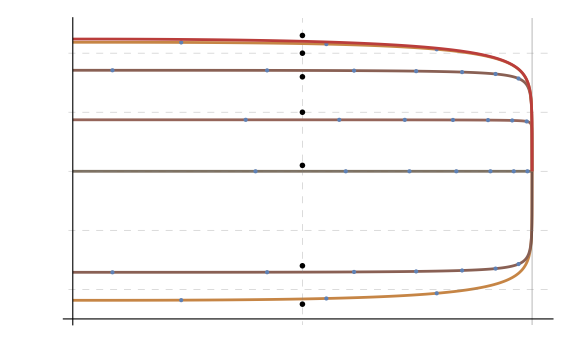

```mathematica
ExportToIMGFolder[DisplayCartesianTPlots[Table[solveEquations[eqOfMotion,u,a,unorm,{},constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->eval,L[0]->0},0,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,L[λ]==0]][[1]],{eval,{-1,-0.1,0,0.01,0.1,1,10}}],Graphics[Style[{Text[MaTeX["e = 0, \\tau_{tot} = \\pi M",Magnification->1.1],{1,1}],
Text[MaTeX["e = 0.01, \\tau_{tot} \\approx 3.10206 M",Magnification->1.1],{1,10}],
Text[MaTeX["e = 0.1, \\tau_{tot} \\approx 2.78391 M",Magnification->1.1],{1,16}],
Text[MaTeX["e = 1, \\tau_{tot} \\approx 4/3 M",Magnification->1.1],{1,20}],
Text[MaTeX["e = 10, \\tau_{tot} \\approx 0.19594 M",Magnification->1.1],{1,23}],
Text[MaTeX["e = -0.1, \\tau_{tot} \\approx 2.78391 M",Magnification->1.1],{1,-16}],
Text[MaTeX["e = -1, \\tau_{tot} = 4/3 M",Magnification->1.1],{1,-22.5}]}]]],
"e-geodesics"]
```

NDSolve::ndsz: At λ == 2.4736, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.13544, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.10834, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

3.15148

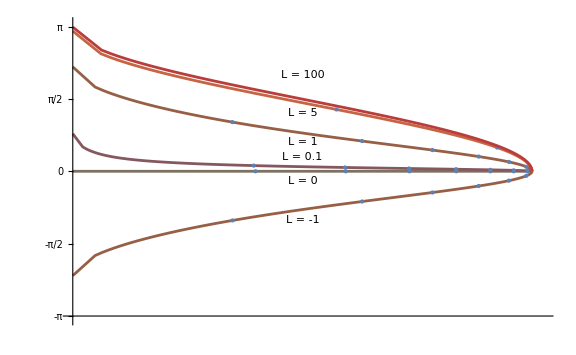

```mathematica
ExportToIMGFolder[DisplayCartesianPhiPlots[Table[solveEquations[eqOfMotion,u,a,unorm,{},constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->eval},0,1,{0,π},And[γt'[λ]==γt''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,e[λ]==0],γϕ][[1]],{eval,{-1,0,0.1,1,5,100}}],Graphics[{
Text["L = -1",{1,-π/3}],
Text["L = 0",{1,-0.2}],
Text["L = 0.1",{1,π/10}],
Text["L = 1",{1,π/5}],
Text["L = 5",{1,π/2-0.3}],
Text["L = 100",{1,2π/3}]}]],
"l-geodesics"]
```

```mathematica
ExportToIMGFolder[DisplayPolarPhiPlots[Table[solveEquations[eqOfMotion,u,a,unorm,{},constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->eval},0,1,{0,π},And[γt'[λ]==γt''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,e[λ]==0],γϕ][[2]],{eval,{-1,0,0.1,1,5,100,10000}}],
Graphics[Style[{Text[MaTeX["L = -1, \\tau_{tot} \\approx 2.47962 M",Magnification->1.1],{0.7,-0.85}],
Text[MaTeX["L = 0, \\tau_{tot} = \\pi M",Magnification->1.1],{0.7,-0.1}],
Text[MaTeX["L = 0.1, \\tau_{tot} \\approx 3.11453 M",Magnification->1.1],{0.4,0.15}],
Rotate[Text[MaTeX["L = 1, \\tau_{tot} \\approx 2.47962 M",Magnification->1.1],{0.7,π/5-0.05}],π/10],
Rotate[Text[MaTeX["L = 5, \\tau_{tot} \\approx 0.89238 M",Magnification->1.1],{0.6,π/2-0.5}],π/15],
Text[MaTeX["L = 100, \\tau_{tot} \\approx 0.04711 M",Magnification->1.1],{0.7,π/2-0.2}]},Bold,FontSize->13]
]
],
"l-geodesics-polar"]
```

NDSolve::ndsz: At λ == 2.4736, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.13544, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.10834, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

9.49885

-Graphics-

```mathematica
Show[Table[solveEquations[eqOfMotion,u,a,unorm,{},constants,{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->eval,L[0]->Lval},0,1,{0,π},And[aϕ[λ]==ar[λ]==at[λ]==0],γϕ][[3]],{eval,{-0.1,0,1}},{Lval,{-1,0,0.1}}],Graphics3D[{Opacity[0.2],Cylinder[{{0,0,25},{0,0,-20}},2],Mesh->All}],PlotRange->{{-2.1,2.1},{-2.1,2.1},Full}]
```

NDSolve::ndsz: At λ == 2.195, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.78368, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.75761, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

5.06867

-Graphics3D-

NDSolve::ndsz: At λ == 1.33032, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.62795, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.63445, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

11.3848

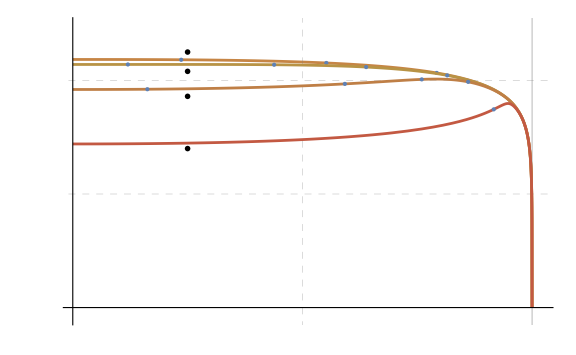

```mathematica
ExportToIMGFolder[DisplayCartesianTPlots[Table[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},aval,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0],γt][[1]],{aval,{0,-0.65,-2.4,-10}}],Graphics[Style[{
Text[MaTeX["\\alpha = -10, \\tau_{tot} \\approx 0.72601 M",Magnification->1.1],{0.5,14}],
Text[MaTeX["\\alpha = -2.4, \\tau_{tot} \\approx 1.63631 M",Magnification->1.1],{0.5,18.6}],
Text[MaTeX["\\alpha = -0.65, \\tau_{tot} \\approx 1.63458 M",Magnification->1.1],{0.5,20.8}],
Text[MaTeX["\\alpha = 0, \\tau_{tot} = 4/3 M",Magnification->1.1],{0.5,22.5}]}]],True],
"e-accel-whole-way-meq1"]
```

NDSolve::ndsz: At λ == 1.20861, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.15443, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.08153, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

7.34846

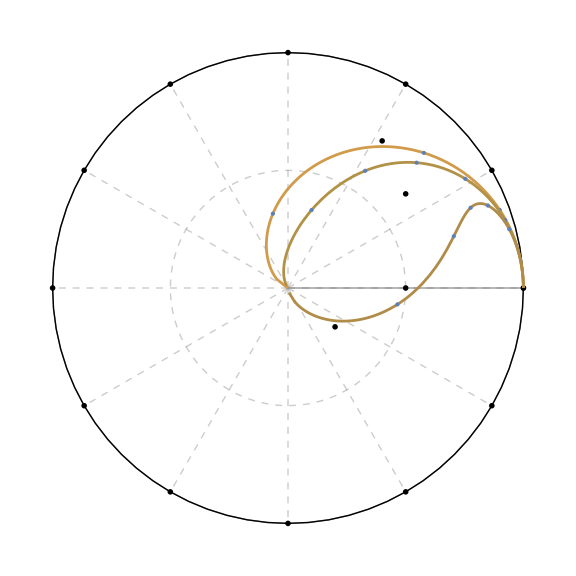

```mathematica
ExportToIMGFolder[DisplayPolarPhiPlots[Table[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[2]],{aval,{0,-0.65,-1.3}}],Graphics[Style[{
Rotate[Text[MaTeX["\\alpha = -1.3, \\tau_{tot} \\approx 2.08303 M",Magnification->1.1],{0.4,-0.33}],0],
Rotate[Text[MaTeX["\\alpha = -0.65, \\tau_{tot} \\approx 2.16171 M",Magnification->1.1],{1,0.8}],0],
Rotate[Text[MaTeX["\\alpha = 0, \\tau_{tot} \\approx 1.21237 M",Magnification->1.1],{0.8,1.25}],0]},Bold,FontSize->13]]],
"l-accel-whole-way"]
```

NDSolve::ndsz: At λ == 1.33032, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1.35367} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.35281} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.35163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::ndsz: At λ == 1.33032, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.62795, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

13.3302

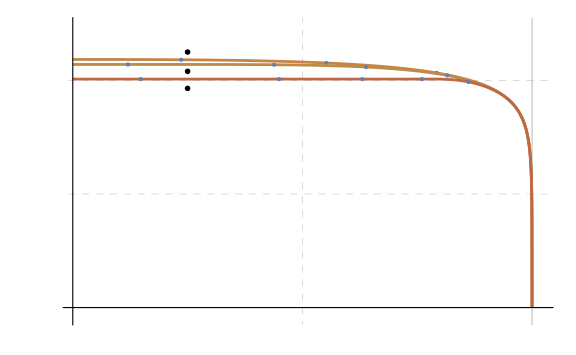

```mathematica
ExportToIMGFolder[DisplayCartesianTPlots[Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},aval,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0],γt][[1]],{aval,{0,-0.65,-2.4}}],
Graphics[Style[{
Text[MaTeX["\\alpha = -2.4, \\tau_{tot} \\approx 2.0537 M",Magnification->1.1],{0.5,19.3}],
Text[MaTeX["\\alpha = -0.65, \\tau_{tot} \\approx 1.63472 M",Magnification->1.1],{0.5,20.8}],
Text[MaTeX["\\alpha = 0, \\tau_{tot} = 4/3 M",Magnification->1.1],{0.5,22.5}]}]],
True],
"e-accel-to-optimal"]
```

NDSolve::ndsz: At λ == 1.20861, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.15443, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.08153, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

8.07885

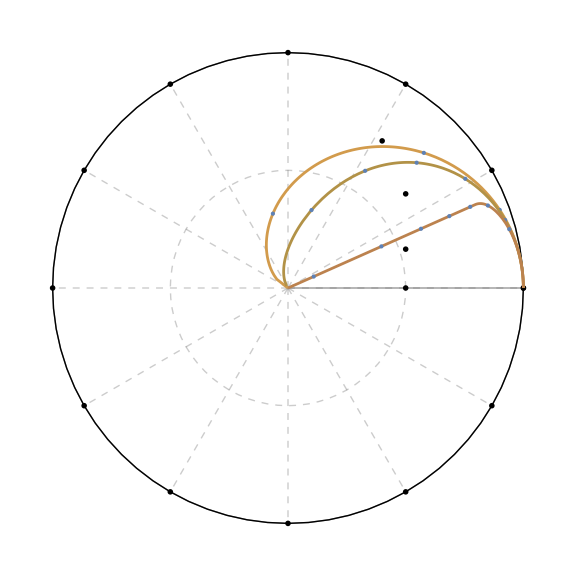

NDSolve::ndsz: At λ == 1.33123, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.15443, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-8.41854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.44364} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolve::ndsz: At λ == 2.17603, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

7.50703

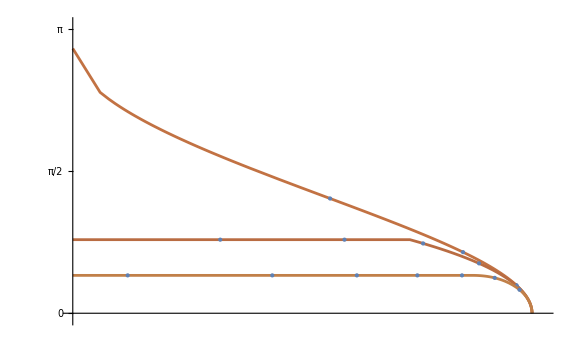

```mathematica
ExportToIMGFolder[
DisplayPolarPhiPlots[
Join[Table[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[2]],{aval,{0,-0.65}}],
Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[2]],{aval,{-1.3}}]],Graphics[Style[{
Rotate[Text[MaTeX["\\alpha = -1.3, \\tau_{tot} \\approx 2.80145 M",Magnification->1.1],{1,0.33}],0],
Rotate[Text[MaTeX["\\alpha = -0.65, \\tau_{tot} \\approx 2.16171 M",Magnification->1.1],{1,0.8}],0],
Rotate[Text[MaTeX["\\alpha = 0, \\tau_{tot} \\approx 1.21237 M",Magnification->1.1],{0.8,1.25}],0]}]]],
"l-accel-to-optimal-polar"
]

ExportToIMGFolder[
DisplayCartesianPhiPlots[
Join[{solveEquations[eqOfMotion,u,a,unorm,{},constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.10},0,1,{0,π},And[γt'[λ]==γt''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,e[λ]==0],γϕ][[1]]},
Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[1]],{aval,{-0.65,-1.3}}]],{},True],
"l-accel-to-optimal"
]
```

## Functions of r for L and e

```mathematica
ColumnForm/@(systemsWhenOneConstantZero={FullSimplify@solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},-0.65,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0],γt][[4]],FullSimplify@solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->2.95},-0.65,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[4]]}/.{γr[λ]->r[]}/.constants/.(unorm/.constants//Simplify))
```

NDSolve::ndsz: At λ == 1.62795, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.58727, step size is effectively zero; singularity or stiff system suspected.

17.3132

{(2 M e[λ] √(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/(r (-2 M+r)^2)-(amag √r √(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/(√(-(e[λ]^2 (2 M-r)^3 r^2)/(-2 M+r)^2+(2 M-r) (L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r))))+γt''[λ]==0
(M e[λ]^2)/(r (-2 M+r))+(M (L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/(r^2 (2 M r-r^2))-(amag e[λ] √r (-2 M+r))/(√(e[λ]^2 r^2 (-2 M+r)-(-2 M+r) (L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r))))+γr''[λ]==0
γt[0]==0
γr[0]==1.99999 M
γϕ[0]==0
γt'[0]==199999.
γr'[0]==-1.,(L[λ]^2 (2 M-r))/r^4+(M (L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/(r^2 (2 M r-r^2))+γr''[λ]==(amag L[λ] (-2 M+r))/(r √(r^2 ((L[λ]^2 (-2 M+r))/r^3+(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r))/r^2)))
-(2 L[λ] √(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/r^4-(amag √(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/(r √(r^2 ((L[λ]^2 (-2 M+r))/r^3+(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r))/r^2)))+γϕ''[λ]==0
γt[0]==0
γr[0]==1.99999 M
γϕ[0]==0
γϕ'[0]==0.737507/M^2
γr'[0]==-(0.00111804 √(8.7025+3.99996 M^2))/M}

```mathematica
{systemsWhenOneConstantZero[[1]]/.L[λ]->0,systemsWhenOneConstantZero[[2]]/.e[λ]->0}//FullSimplify
```

1.6478

{{2 M e[λ] √(-1+e[λ]^2+(2 M)/r)+(-2 M+r) (amag √(r (2 M+(-1+e[λ]^2) r))+(-2 M+r) γt''[λ])==0,M+r^2 (amag e[λ]+γr''[λ])==0,γt[0]==0,γr[0]==1.99999 M,γϕ[0]==0,γt'[0]==199999.,γr'[0]==-1.},{3 M L[λ]^2+M r^2+amag L[λ] √((2 M-r) r^5)+r^4 γr''[λ]==L[λ]^2 r,r^2 γϕ''[λ]==amag √(L[λ]^2+r^2)+(2 L[λ] √((2 M-r) (L[λ]^2+r^2)))/r^(5/2),γt[0]==0,γr[0]==1.99999 M,γϕ[0]==0,γϕ'[0]==0.737507/M^2,γr'[0]==-(0.00111804 √(8.7025+3.99996 M^2))/M}}

For the L=0 system, there is a relation when accelerating de/dr= (g_tt a^t)/u^r=-|a| (obtained by differentiating de/dτ and doing the trick with extracting u^r) which after integration gives e(r)=-a r+C; from e_0=e(2M)= -2M a + C we get C = e_0+2M a.

So e(r) = e_0+ 2M a - a r which we can insert into equation 2 from L=0 set.

We get an elliptic integral with the following polynomial:

```mathematica
Roots[m y^3+c y^2-y aa (e0 + 2m aa) + aa^2/2==0/.{m->1,aa->-0.65,e0->1},y]//FullSimplify
```

10.6932

y==1/6 (-2 c+(1.47411+2.51984 c^2)/((-5.70375-1.755 c-2. c^3+√(31.732+c (20.0202+c (-1.02667+22.815 c))))^(1/3))+2^(2/3) (-5.70375-1.755 c-2. c^3+√(31.732+c (20.0202+c (-1.02667+22.815 c))))^(1/3))||c/3+((0.209987+0.363708 ⅈ) (0.585+c^2))/((-5.70375-1.755 c-2. c^3+√(31.732+c (20.0202+c (-1.02667+22.815 c))))^(1/3))+(0.132283-0.229122 ⅈ) (-5.70375-1.755 c-2. c^3+√(31.732+c (20.0202+c (-1.02667+22.815 c))))^(1/3)+y==0.||c/3+((0.209987-0.363708 ⅈ) (0.585+c^2))/((-5.70375-1.755 c-2. c^3+√(31.732+c (20.0202+c (-1.02667+22.815 c))))^(1/3))+1/3 (-1/2)^(1/3) (-5.70375-1.755 c-2. c^3+√(31.732+c (20.0202+c (-1.02667+22.815 c))))^(1/3)+y==0.

Equations describing changes in e/L with respect to local r:

```mathematica
(Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify)/.(Solve[unorm/.γt'[λ]->0/.Rule->Equal,γϕ'[λ]])//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{aϕ[λ]→-(amag γr'[λ])/(√((2 M-r) r)),ar[λ]→amag √(1-(2 M)/r+γr'[λ]^2)},{aϕ[λ]→-(amag γr'[λ])/(√((2 M-r) r)),ar[λ]→-amag √(1-(2 M)/r+γr'[λ]^2)}}

```mathematica
(Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify)/.(Solve[unorm/.γϕ'[λ]->0/.Rule->Equal,γt'[λ]])//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{at[λ]→(amag r γr'[λ])/(-2 M+r),ar[λ]→amag √(1-(2 M)/r+γr'[λ]^2)},{at[λ]→(amag r γr'[λ])/(-2 M+r),ar[λ]→-amag √(1-(2 M)/r+γr'[λ]^2)}}

```mathematica
lr=-(Integrate[(y aa)/Sqrt[(2 m)/y-1],y]//FullSimplify)+L0
```

L0-aa (-1/2 √(-1+(2 m)/y) y (3 m+y)-3 m^2 ArcTan[√(-1+(2 m)/y)])

```mathematica
er=-aa y +2 m aa + e0
```

e0+2 aa m-aa y

Let’s verify that our functions make sense by comparing to numerical calculations:

NDSolve::ndsz: At λ == 1.63376, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.6339, step size is effectively zero; singularity or stiff system suspected.

4.16993

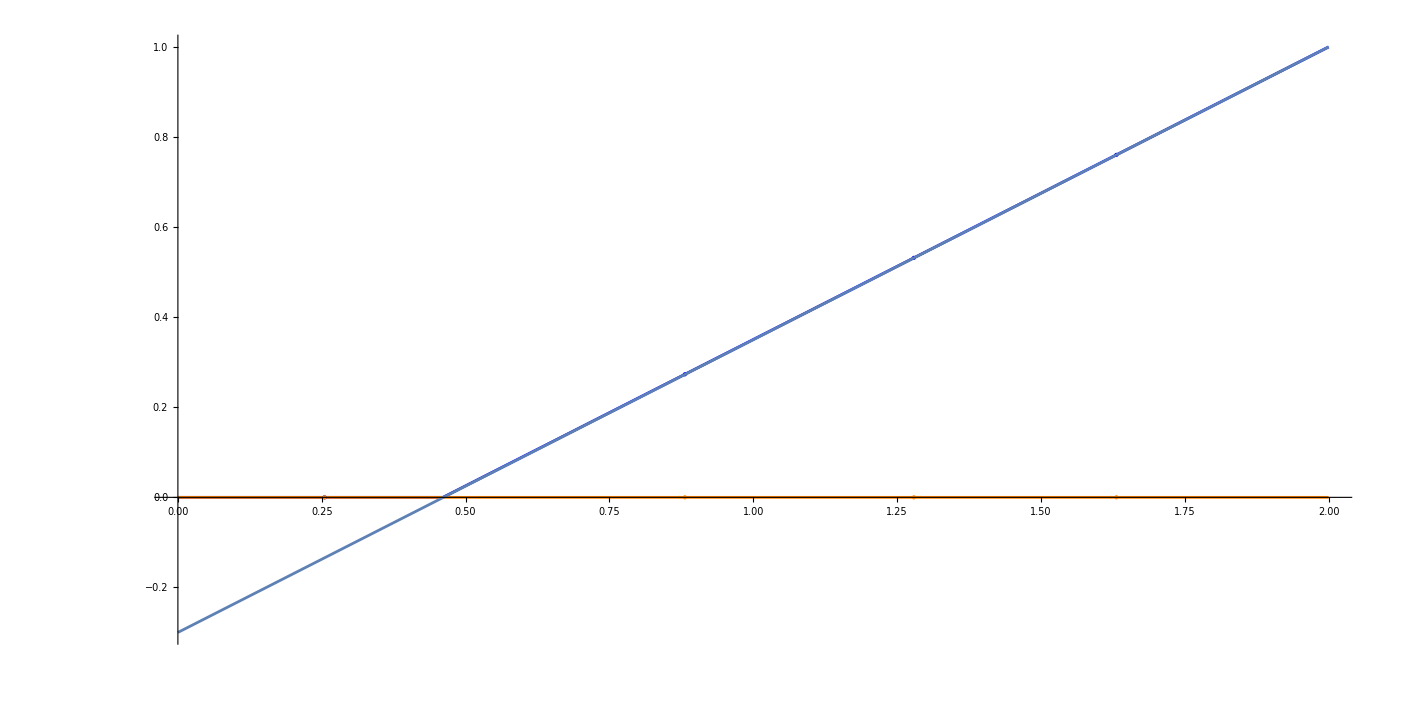

```mathematica
Show[{solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.9999M,γϕ[0]->0},{e[0]->1,L[0]->0},-0.65,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0],γt][[5]],Plot[-aa y +1.9999 m aa + e0/.{e0->1,aa->-0.65,m->1},{y,0,2}]},PlotRange->{{0,2},All},Axes->{False,True}]
```

NDSolve::ndsz: At λ == 2.31533, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.79102, step size is effectively zero; singularity or stiff system suspected.

3.47037

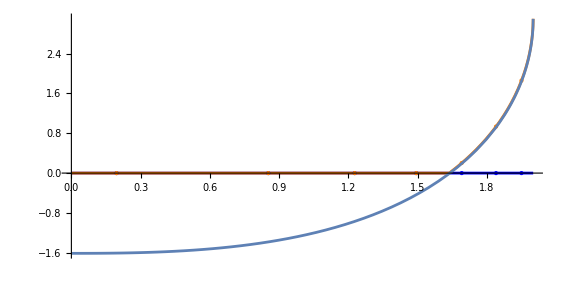

```mathematica
Show[{solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.10},-1,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[5]],Plot[lr/.{L0->3.10,aa->-1,m->1},{y,0,2 m}/.m->1]},PlotRange->{{0,2},All},Axes->{False,True}]
```

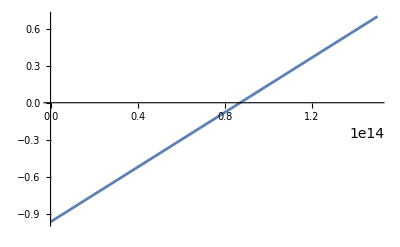

```mathematica
Plot[-aa y +2 m aa + e0/.{e0->0.7,aa->-1/90000000000000,m->1500*5*10^10},{y,0,2 m/.{m->1500*5*10^10}}]
```

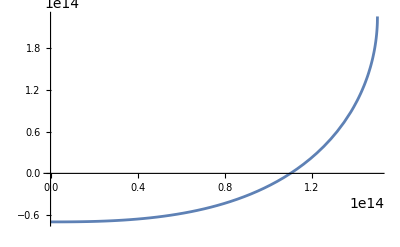

```mathematica
Plot[lr/.{L0->3m,aa->-1/90000000000000}/.{m->1500*5*10^10},{y,0,2 m/.{m->1500*5*10^10}}]
```

Let’s input our elliptical integral for dτ in the radial case, made by inserting the e(r) and l(r)=0 functions into the expression for proper time -∫_(2M)^0 ⅆr/(√((e(r))^2-(1+(L(r))^2/r^2)(1-(2M)/r)))

```mathematica
Collect[e^2-(1+l^2/y^2)(1-(2m)/y)/.{l->0,e->er},y]
```

-1+e0^2+4 aa e0 m+4 aa^2 m^2+(2 m)/y+(-2 aa e0-4 aa^2 m) y+aa^2 y^2

To transform this integral, we need to perform the substitution r = 1/z, ⅆr =- 1/z^2ⅆu giving us in the square root (after absorbing one z into the root):

```mathematica
Collect[z^2(e^2-(1+l^2/y^2)(1-(2m)/y))/.{l->0,e->er}/.y->1/z,z]
```

aa^2+(-2 aa e0-4 aa^2 m) z+(-1+e0^2+4 aa e0 m+4 aa^2 m^2) z^2+2 m z^3

Therefore, the integral ⅆτ= ∫_(1/(2M))^∞ ⅆz/(z √(2M z^3+C_2 z^2+C_1 z+a^2)).

## Useless leftovers.

```mathematica
solveEquationsTotal[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,atmagnitude_,aϕmagnitude_,mass_,λrange_List,assumptions_,plotfunc_:γt,debug_:True]:=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->atmagnitude},{γt,γr,γϕ},Join[{λ},λrange]];
If[debug,
Print[Simplify/@{unorm,constants,eqs}];
Print[Simplify@(eqTable/.unorm)/.r[]->γr[λ]/.M->mass];
Print[ustart];
Print[aeqs];
Print[system//Simplify];
Print[solution];
];
Return[{ParametricPlot[{γr[λ],plotfunc[λ](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5],
ParametricPlot[{γr[λ] * Cos[plotfunc[λ]],γr[λ] * Sin[plotfunc[λ]](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1],
ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Boxed->False],
system
}]
];
```

```mathematica
solveEquationsTotal[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.plane/.r[]->γr[λ],{at[λ],aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants,{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->3.5},0,-1,1,{0,π},{},γϕ]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

NDSolve::underdet: There are more dependent variables, {at[λ],γr[λ],γt[λ],γϕ[λ]}, than equations, so the system is underdetermined.

{{γr'[λ]→-(√((2 M-r) (r+(2 M-r) γt'[λ]^2+r^3 γϕ'[λ]^2)))/r},{γϕ'[λ]→L[λ]/r^2,γt'[λ]→(e[λ] r)/(2 M-r)},●
●
0
-aϕ[λ]+(2 γr'[λ] γϕ'[λ])/r+γϕ''[λ] | α
 }

{(2 γt'[λ] √((γr[λ]+(2-γr[λ]) γt'[λ]^2+γr[λ]^3 γϕ'[λ]^2)/(2-γr[λ])))/γr[λ]^2+γt''[λ]==at[λ],1/γr[λ]^2+(3-γr[λ]) γϕ'[λ]^2+γr''[λ]==ar[λ],True,γϕ''[λ]==aϕ[λ]+(2 γϕ'[λ] √((2-γr[λ]) (γr[λ]+(2-γr[λ]) γt'[λ]^2+γr[λ]^3 γϕ'[λ]^2)))/γr[λ]^2}

{γϕ'[0]→0.875009/M^2,γt'[0]→199999.,γr'[0]→-(0.500003 √(0.0000612503+3.99998 M^2))/M}

{aϕ[λ]→(at[λ] γr[λ]^3 (-2 M+γr[λ])^2 γt'[λ] γϕ'[λ]+√(γr[λ]^5 γr'[λ]^2 (amag^2 γr[λ]^3 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)+at[λ]^2 (2 M-γr[λ]) (4 M^2 γt'[λ]^2+γr[λ] (-4 M γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2-γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2))))))/(γr[λ]^5 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)),ar[λ]→((2 M-γr[λ]) (at[λ] (2 M-γr[λ]) γr[λ]^2 γr'[λ]^2 γt'[λ]+γϕ'[λ] √(γr[λ]^5 γr'[λ]^2 (amag^2 γr[λ]^3 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)+at[λ]^2 (2 M-γr[λ]) (4 M^2 γt'[λ]^2+γr[λ] (-4 M γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2-γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)))))))/(γr[λ]^4 (γr'[λ]^3+γr[λ] (-2 M+γr[λ]) γr'[λ] γϕ'[λ]^2))}

{(2 M γr'[λ] γt'[λ])/(γr[λ] (-2 M+γr[λ]))+γt''[λ]==at[λ],(M γr'[λ]^2)/(2 M γr[λ]-γr[λ]^2)+(M (-2 M+γr[λ]) γt'[λ]^2)/γr[λ]^3+(2 M-γr[λ]) γϕ'[λ]^2+γr''[λ]==((2 M-γr[λ]) (at[λ] (2 M-γr[λ]) γr[λ]^2 γr'[λ]^2 γt'[λ]+γϕ'[λ] √(γr[λ]^5 γr'[λ]^2 (amag^2 γr[λ]^3 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)+at[λ]^2 (2 M-γr[λ]) (4 M^2 γt'[λ]^2+γr[λ] (-4 M γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2+(2 M-γr[λ]) γr[λ] γϕ'[λ]^2)))))))/(γr[λ]^4 (γr'[λ]^3+γr[λ] (-2 M+γr[λ]) γr'[λ] γϕ'[λ]^2)),(2 γr'[λ] γϕ'[λ])/γr[λ]+γϕ''[λ]==(at[λ] γr[λ]^3 (-2 M+γr[λ])^2 γt'[λ] γϕ'[λ]+√(γr[λ]^5 γr'[λ]^2 (amag^2 γr[λ]^3 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)+at[λ]^2 (2 M-γr[λ]) (4 M^2 γt'[λ]^2+γr[λ] (-4 M γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2+(2 M-γr[λ]) γr[λ] γϕ'[λ]^2))))))/(γr[λ]^5 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)),γt[0]==0,M==0.500003 γr[0],γϕ[0]==0,M^2 γϕ'[0]==0.875009,γt'[0]==199999.,√(7.34641×10^10+4.79761×10^15 M^2)+6.92646×10^7 M γr'[0]==0}

NDSolve[{(2 γr'[λ] γt'[λ])/((-2+γr[λ]) γr[λ])+γt''[λ]==at[λ],γr'[λ]^2/(2 γr[λ]-γr[λ]^2)+((-2+γr[λ]) γt'[λ]^2)/γr[λ]^3+(2-γr[λ]) γϕ'[λ]^2+γr''[λ]==((2-γr[λ]) (at[λ] (2-γr[λ]) γr[λ]^2 γr'[λ]^2 γt'[λ]+γϕ'[λ] √(at[λ]^2 (2-γr[λ]) γr[λ]^5 γr'[λ]^2 (4 γt'[λ]^2+γr[λ] (-4 γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2+(2-γr[λ]) γr[λ] γϕ'[λ]^2))))))/(γr[λ]^4 (γr'[λ]^3+(-2+γr[λ]) γr[λ] γr'[λ] γϕ'[λ]^2)),(2 γr'[λ] γϕ'[λ])/γr[λ]+γϕ''[λ]==(at[λ] (-2+γr[λ])^2 γr[λ]^3 γt'[λ] γϕ'[λ]+√(at[λ]^2 (2-γr[λ]) γr[λ]^5 γr'[λ]^2 (4 γt'[λ]^2+γr[λ] (-4 γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2+(2-γr[λ]) γr[λ] γϕ'[λ]^2)))))/(γr[λ]^5 (γr'[λ]^2+(-2+γr[λ]) γr[λ] γϕ'[λ]^2)),γt[0]==0,γr[0]==1.99999,γϕ[0]==0,γϕ'[0]==0.875009,γt'[0]==199999.,γr'[0]==-1.00001},{γt,γr,γϕ},{λ,0,π}]

ReplaceAll::reps: {NDSolve[{(2 γr'[λ] γt'[λ])/(Plus[«2»] γr[«1»])+γt''[λ]==at[λ],«7»,γr'[0]==-1.00001},{γt,γr,γϕ},{λ,0,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Last::normal: Nonatomic expression expected at position 1 in Last[γϕ].

ReplaceAll::reps: {NDSolve[{(2 γr'[λ] γt'[λ])/(Plus[«2»] γr[«1»])+γt''[λ]==at[λ],«7»,γr'[0]==-1.00001},{γt,γr,γϕ},{λ,0,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Last::normal: Nonatomic expression expected at position 1 in Last[γϕ].

ReplaceAll::reps: {NDSolve[{(2 γr'[λ] γt'[λ])/(Plus[«2»] γr[«1»])+γt''[λ]==at[λ],«7»,γr'[0]==-1.00001},{γt,γr,γϕ},{λ,0,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[γϕ].

General::stop: Further output of Last::normal will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

ParametricPlot3D::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot3D::plln will be suppressed during this calculation.

6.87122

Last::normal: Nonatomic expression expected at position 1 in Last[γϕ].

General::stop: Further output of Last::normal will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

ParametricPlot3D::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

ParametricPlot3D::plln: Limiting value Last[γϕ] in {λ,0,Last[γϕ]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot3D::plln will be suppressed during this calculation.

{ParametricPlot[{γr[λ],γϕ[λ]}/.solution,{λ,0,Last[Last[ResourceFunction[InterpolatingFunctionDomain][First[γϕ/.solution]]]]},ColorFunction→Function[{x,y,par},ColorData[DarkRainbow][1-par/π]],ColorFunctionScaling→False,Mesh→{Range[0,π,π/8]},MeshStyle→Directive[PointSize[Medium]],AspectRatio→0.5],ParametricPlot[{γr[λ] Cos[γϕ[λ]],γr[λ] Sin[γϕ[λ]]}/.solution,{λ,0,Last[Last[ResourceFunction[InterpolatingFunctionDomain][First[γϕ/.solution]]]]},ColorFunction→Function[{x,y,par},ColorData[DarkRainbow][1-par/π]],ColorFunctionScaling→False,Mesh→{Range[0,π,π/8]},MeshStyle→Directive[PointSize[Medium]],AspectRatio→1],ParametricPlot3D[{γr[λ] Cos[γϕ[λ]],γr[λ] Sin[γϕ[λ]],γt[λ]}/.solution,{λ,0,Last[Last[ResourceFunction[InterpolatingFunctionDomain][First[γϕ/.solution]]]]},ColorFunction→Function[{x,y,z,par},ColorData[DarkRainbow][1-par/π]],ColorFunctionScaling→False,Mesh→{Range[0,π,π/8]},MeshStyle→Directive[PointSize[Medium]],BoxRatios→{1,1,1},Boxed→False],{(2 M γr'[λ] γt'[λ])/(γr[λ] (-2 M+γr[λ]))+γt''[λ]==at[λ],(M γr'[λ]^2)/(2 M γr[λ]-γr[λ]^2)+(M (-2 M+γr[λ]) γt'[λ]^2)/γr[λ]^3+(2 M-γr[λ]) γϕ'[λ]^2+γr''[λ]==((2 M-γr[λ]) (at[λ] (2 M-γr[λ]) γr[λ]^2 γr'[λ]^2 γt'[λ]+γϕ'[λ] √(γr[λ]^5 γr'[λ]^2 (amag^2 γr[λ]^3 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)+at[λ]^2 (2 M-γr[λ]) (4 M^2 γt'[λ]^2+γr[λ] (-4 M γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2+(2 M-γr[λ]) γr[λ] γϕ'[λ]^2)))))))/(γr[λ]^4 (γr'[λ]^3+γr[λ] (-2 M+γr[λ]) γr'[λ] γϕ'[λ]^2)),(2 γr'[λ] γϕ'[λ])/γr[λ]+γϕ''[λ]==(at[λ] γr[λ]^3 (-2 M+γr[λ])^2 γt'[λ] γϕ'[λ]+√(γr[λ]^5 γr'[λ]^2 (amag^2 γr[λ]^3 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)+at[λ]^2 (2 M-γr[λ]) (4 M^2 γt'[λ]^2+γr[λ] (-4 M γt'[λ]^2+γr[λ] (-γr'[λ]^2+γt'[λ]^2+(2 M-γr[λ]) γr[λ] γϕ'[λ]^2))))))/(γr[λ]^5 (γr'[λ]^2+γr[λ] (-2 M+γr[λ]) γϕ'[λ]^2)),γt[0]==0,γr[0]==1.99999 M,γϕ[0]==0,γϕ'[0]==0.875009/M^2,γt'[0]==199999.,γr'[0]==-(0.500003 √(0.0000612503+3.99998 M^2))/M}}

```mathematica
Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0,}/.plane/.r[]->γr[λ],{at[λ],aϕ[λ],ar[λ]}][[1]]
```

Solve::naqs: … is not a quantified system of equations and inequalities.

{(at[λ]^2 (2 M-γr[λ]))/γr[λ]-(ar[λ]^2 γr[λ])/(2 M-γr[λ])+aϕ[λ]^2 γr[λ]^2==amag^2,-(ar[λ] γr[λ] γr'[λ])/(2 M-γr[λ])+(at[λ] (2 M-γr[λ]) γt'[λ])/γr[λ]+aϕ[λ] γr[λ]^2 γϕ'[λ]==0,Null}

```mathematica
{a[α] a[-α]==amag^2,a[α] u[-α]==0}
```

{(at[λ]^2 (2 M-r))/r-(ar[λ]^2 r)/(2 M-r)+aϕ[λ]^2 r^2 Sin[θ]^2==amag^2,-(ar[λ] r γr'[λ])/(2 M-r)+(at[λ] (2 M-r) γt'[λ])/r+aϕ[λ] r^2 Sin[θ]^2 γϕ'[λ]==0}